## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
data=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/6sem/6115/tables/data.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data//TableForm
```

№ | U, | U | I
1. | 1. | 0.0001 | 0.01
2. | 9. | 0.0009 | 0.145
3. | 15. | 0.0015 | 0.255
4. | 20. | 0.002 | 0.348
5. | 29. | 0.0029 | 0.504
6. | 36. | 0.0036 | 0.639
7. | 43. | 0.0043 | 0.761
8. | 48. | 0.0048 | 0.845
9. | 59. | 0.0059 | 1.028
10. | 68. | 0.0068 | 1.169
11. | 78. | 0.0078 | 1.32
12. | 87. | 0.0087 | 1.46
13. | 96. | 0.0096 | 1.604
14. | 110. | 0.011 | 1.817
15. | 119. | 0.0119 | 1.94
16. | 133. | 0.0133 | 2.135
17. | 148. | 0.0148 | 2.333
18. | 162. | 0.0162 | 2.511
19. | 175. | 0.0175 | 2.68
20. | 187. | 0.0187 | 2.823
21. | 207. | 0.0207 | 3.042
22. | 225. | 0.0225 | 3.231
23. | 240. | 0.024 | 3.384
24. | 254. | 0.0254 | 3.521
25. | 274. | 0.0274 | 3.703
26. | 300. | 0.03 | 3.912
27. | 326. | 0.0326 | 4.105
28. | 371. | 0.0371 | 4.378
29. | 405. | 0.0405 | 4.563
30. | 1978. | 0.1978 | 1.7
31. | 2011. | 0.2011 | 1.724
32. | 2161. | 0.2161 | 1.808
33. | 2295. | 0.2295 | 1.934
34. | 2332. | 0.2332 | 1.975
35. | 2425. | 0.2425 | 2.095
36. | 2528. | 0.2528 | 2.233
37. | 2645. | 0.2645 | 2.347
38. | 2749. | 0.2749 | 2.352
39. | 2928. | 0.2928 | 2.405
40. | 3498. | 0.3498 | 0.385
41. | 3628. | 0.3628 | 0.386
42. | 3698. | 0.3698 | 0.39
43. | 3770. | 0.377 | 0.397
44. | 3881. | 0.3881 | 0.416
45. | 4034. | 0.4034 | 0.464
46. | 4210. | 0.421 | 0.57
47. | 4393. | 0.4393 | 0.785
48. | 4537. | 0.4537 | 1.091
49. | 4699. | 0.4699 | 1.692
50. | 4858. | 0.4858 | 2.672
51. | 4974. | 0.4974 | 3.871
52. | 5005. | 0.5005 | 4.267

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFit=data⟦2;;,{1,4}⟧;
fit=LinearModelFit[forFit,{1,x},x]
fit@"ParameterTable"
Plot[fit["Function"]@x, {x, 0, 32}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

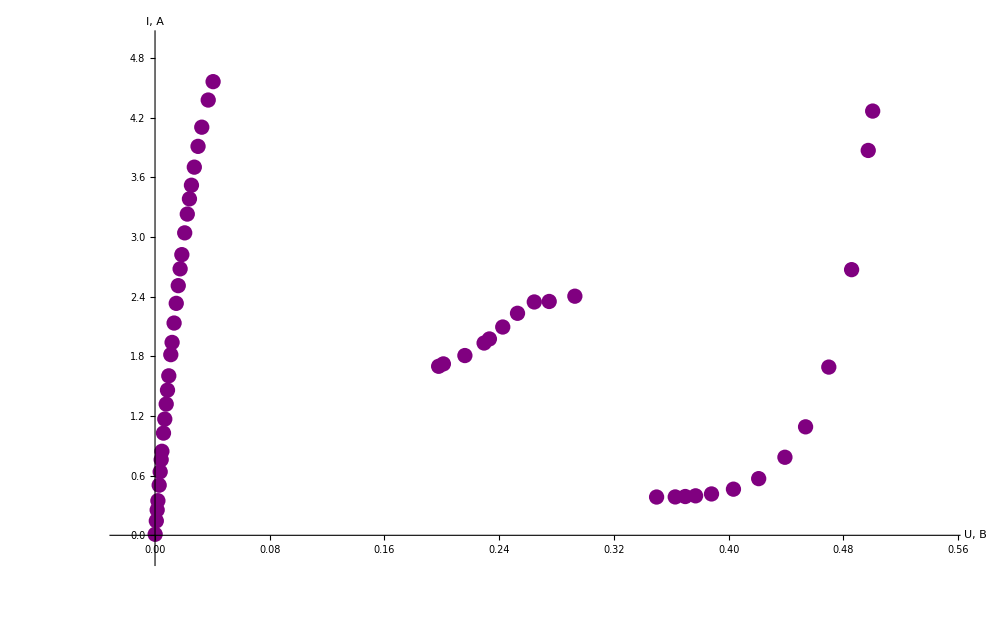

```mathematica
Show[ListPlot[data⟦2;;,{3,4}⟧,
GridLines->{grids@0.01,grids@0.2},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"U, В","I, A"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{-0.02,0.55},{-0.2,4.97}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,4,5,5}⟧,
GridLines->{grids@0.5,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,6.9},{0,15}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```